```mathematica
ClearAll["Global`*"]
```

## Experimental data

```mathematica
Amass={76.00000 ,82.00000,96.00000,100.00000,116.00000,128.00000,130.00000,150.00000};
beta={0.26151,0.12780,0.13228,0.17318,0.07922,0.12322,0.13358,0.09559};
betaExp={0.26271,0.16832,0.13492,0.00855,0.08237,0.14515,0.12938,0.13084};
dkratio={0.19000,0.02200,0.10000,0.16700,0.40000,0.21250,0.17500,0.69700};
t1=Table[{Amass[[i]],beta[[i]]},{i,1,Length[Amass]}];
t2=Table[{Amass[[i]],betaExp[[i]]},{i,1,Length[Amass]}];
t3=Table[{Amass[[i]],dkratio[[i]]},{i,1,Length[Amass]}];
```

## Plots

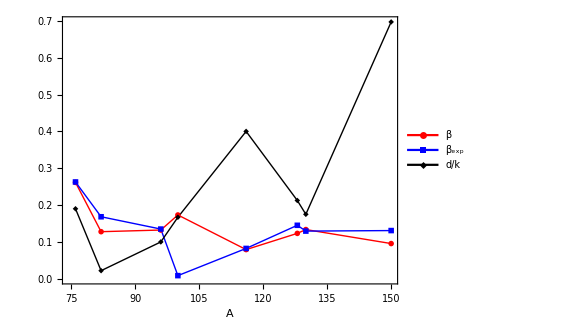

```mathematica
myfig=ListPlot[{t1,t2,t3},Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,Joined->True,PlotMarkers->{Automatic,Scaled[0.035]},PlotRange->All,ImageSize->420,LabelStyle->{22,Bold,Black,FontFamily->"Times"},FrameLabel->{"A"},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick}},PlotLegends->Placed[{"β","β_exp","d/k"},{0.2,0.7}],FrameTicks->{{Automatic,Automatic},{Table[i,{i,75,150,15}],Table[i,{i,75,150,15}]}},FrameTicksStyle->{{Black,Black},{Black,{Black,FontOpacity->0,FontSize->0}}}];
Export["/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/beta-coeff-plot.pdf",Show[myfig],ImageResolution->1200];
myfig
```